## Critical surfaces, h and j for axisymmetric coils

```mathematica
Clear["Global`*"]
Clear[R,z,a,mu0,alphaSqrd1,alphaSqrd2,betaSqrd1,betaSqrd2,m,fieldAxial, fieldRadial,fieldMag,dfieldMagdR,dfieldMagdZ,dfieldMagds];
(*a=1;
mu0=1.25663706 10^-6;(*m kg s-2 A-2*)
current=10^3;*)
a = 5;
current1=1*(π/mu0);
current2 = 1.5*(π/mu0);
const1=(mu0*current1)/π;
const2 = (mu0*current2)/π;
z1 = -7;
z2 = 7;
alphaSqrd1[R_,z_]:=a^2+R^2+(z-z1)^2-2 *a* R;
betaSqrd1[R_,z_]:=a^2+R^2+(z-z1)^2+2*a*R;
m1[R_,z_]:=1-alphaSqrd1[R,z]/betaSqrd1[R,z];
alphaSqrd2[R_,z_]:=a^2+R^2+(z-z2)^2-2 *a* R;
betaSqrd2[R_,z_]:=a^2+R^2+(z-z2)^2+2*a*R;
m2[R_,z_]:=1-alphaSqrd2[R,z]/betaSqrd2[R,z];
fieldRadial[R_,z_]:=((const1*(z-z1))/(2*alphaSqrd1[R,z]*Sqrt[betaSqrd1[R,z]]*R))*((a^2+R^2+(z-z1)^2)*EllipticE[m1[R,z]]-alphaSqrd1[R,z]*EllipticK[m1[R,z]]) + ((const2*(z-z2))/(2*alphaSqrd2[R,z]*Sqrt[betaSqrd2[R,z]]*R))*((a^2+R^2+(z-z2)^2)*EllipticE[m2[R,z]]-alphaSqrd2[R,z]*EllipticK[m2[R,z]]);
fieldAxial[R_,z_]:=((const1)/(2*alphaSqrd1[R,z]*Sqrt[betaSqrd1[R,z]]))*((a^2-R^2-(z-z1)^2)*EllipticE[m1[R,z]]+alphaSqrd1[R,z]*EllipticK[m1[R,z]]) + ((const2)/(2*alphaSqrd2[R,z]*Sqrt[betaSqrd2[R,z]]))*((a^2-R^2-(z-z2)^2)*EllipticE[m2[R,z]]+alphaSqrd2[R,z]*EllipticK[m2[R,z]]);
fieldMagSqrd[R_,z_]=Dot[{fieldRadial[R,z],fieldAxial[R,z]},{fieldRadial[R,z],fieldAxial[R,z]}] ;
dfieldMagSqrddR[R_,z_] = D[fieldMagSqrd[R,z],R];
dfieldMagSqrddZ[R_,z_] = D[fieldMagSqrd[R,z],z];
dfieldMagds[R_,z_] =0.5*(fieldRadial[R,z]*dfieldMagSqrddR[R,z]+ fieldAxial[R,z]*dfieldMagSqrddZ[R,z])/fieldMagSqrd[R,z];
bHat[R_,z_] = {fieldRadial[R,z],fieldAxial[R,z]}/Sqrt[fieldMagSqrd[R,z]];
d2fieldMagds2[R_,z_] = 0.5*(fieldMagSqrd[R,z]*( Sqrt[fieldMagSqrd[R,z]]*Laplacian[fieldMagSqrd[R,z],{R,z}] + Dot[Grad[fieldMagSqrd[R,z],{R,z}],(fieldRadial[R,z]/Sqrt[fieldMagSqrd[R,z]])*D[{fieldRadial[R,z],fieldAxial[R,z]},R]+(fieldAxial[R,z]/Sqrt[fieldMagSqrd[R,z]])*D[{fieldRadial[R,z],fieldAxial[R,z]},z]] ) - 2*(Sqrt[fieldMagSqrd[R,z]]*dfieldMagds[R,z])*Dot[{fieldRadial[R,z],fieldAxial[R,z]},Grad[fieldMagSqrd[R,z],{R,z}]])/fieldMagSqrd[R,z]^2;
```

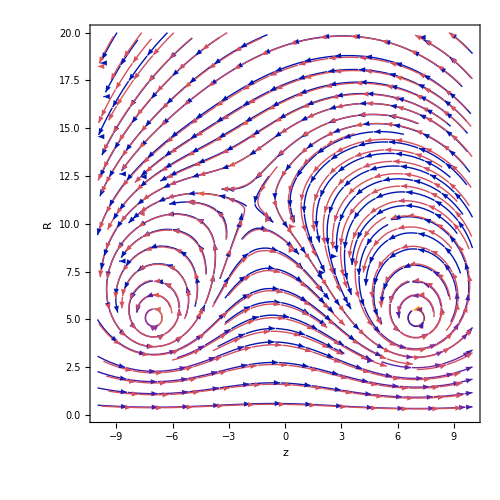

```mathematica
nZ = 10.;
nR = 20.;
bplot = StreamPlot[{fieldAxial[R,z],fieldRadial[R,z]},{z,-nZ,nZ},{R,0,nR},FrameLabel->{z,R},StreamColorFunction->Automatic,LabelStyle->{15,GrayLevel[0]},ImageSize->500]; bhatplot = StreamPlot[{fieldAxial[R,z],fieldRadial[R,z]}/Sqrt[fieldMagSqrd[R,z]],{z,-nZ,nZ},{R,0,nR},FrameLabel->{z,R},StreamColorFunction->Automatic,LabelStyle->{15,GrayLevel[0]},ImageSize->500];
Show[bplot,bhatplot]
(*cplot = ContourPlot[Sqrt[fieldMagSqrd[R,z]],{z,-nZ,nZ},{R,0,nR},PlotPoints->50,FrameLabel->{z,R},Contours->200,PlotLegends->Automatic,LabelStyle->{15,GrayLevel[0]},ImageSize->500]*)
(*Export["/Users/OptimusPrime/Documents/magnetic-mirror/magnetic_field_coils.pdf",splot]
Export["/Users/OptimusPrime/Documents/magnetic-mirror/mag_magnetic_field_coils.png",cplot,ImageResolution->4*72]*)
```

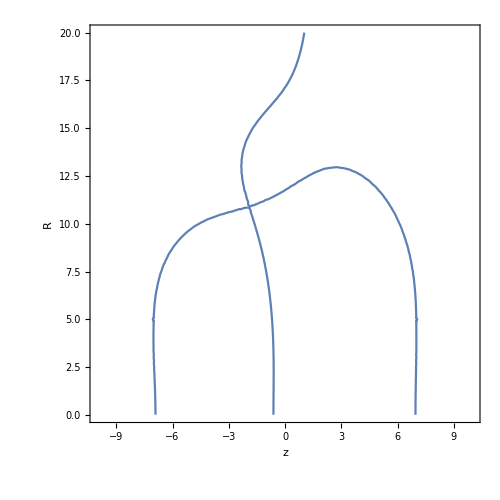

```mathematica
nZ = 10.;
nR = 20.;
fieldMagSqrd[0.01,0];
dfieldMagds[0.01,7];
sigmaplot = ContourPlot[dfieldMagds[R,z] == 0,{z,-nZ,nZ},{R,0,nR},PlotPoints->30,FrameLabel->{z,R,"",""},Contours->200,PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"d|B|/ds"],Right]},LabelStyle->{20,GrayLevel[0]},ImageSize->500]
(*signplot = ContourPlot[d2fieldMagds2[R,z] ,{z,-nZ,nZ},{R,0,5},PlotPoints->30,FrameLabel->{z,R,"",""},Contours->200,PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"|B|''"],Right]},LabelStyle->{20,GrayLevel[0]},ImageSize->500]*)
(*Export["/Users/OptimusPrime/Documents/magnetic-mirror/Sigma_pm_equalcurrentsradius.pdf",sigmaplot]*)
(*Evaluate[dfieldMagds[R,z] == 0,{z,-nZ,nZ},{R,0,nR}]*)
(*SigmaRight  = Table[With[{R =rFix}, FindRoot[dfieldMagds[R,z] == 0,{{z,7}}]],{rFix,0.001,nR,0.2}]
SigmaCenter  = Table[With[{R =rFix}, FindRoot[dfieldMagds[R,z] == 0,{{z,0}}]],{rFix,0.001,nR,0.2}]*)
```

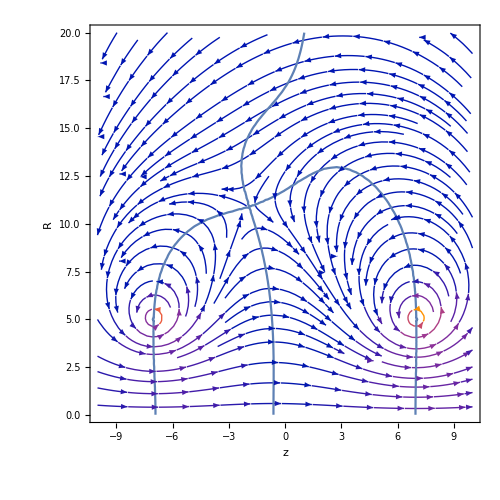

```mathematica
Show[bplot,sigmaplot]
```

```mathematica
nZ = 10.;
nR = 20.;
fieldMag3D = Plot3D[Sqrt[fieldMagSqrd[R,z]],{z,-nZ,nZ},{R,0,nR},AxesLabel->{"z","R","|B|"},LabelStyle->{20,GrayLevel[0]},ImageSize->500]
(*Export["/Users/OptimusPrime/Documents/magnetic-mirror/fieldmag3D.pdf",fieldMag3D]*)
```

-Graphics3D-

/Users/OptimusPrime/Documents/magnetic-mirror/fieldmag3D.pdf

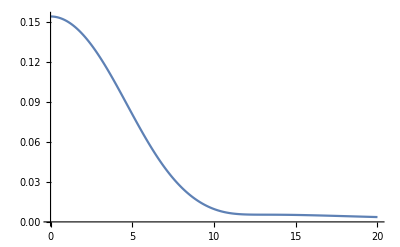

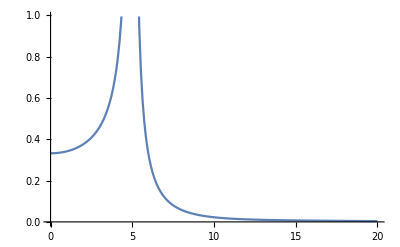

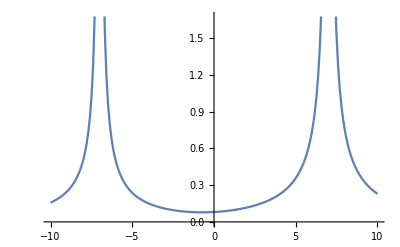

```mathematica
nZ = 10.;
nR = 20.;
(*cplotd2ds2= ContourPlot[d2fieldMagds2[R,z] ,{z,-nZ,nZ},{R,0,nR},FrameLabel->{z,R},Contours->200,ImageSize->500]*)
(*dfieldMagds[0.1,0]*) 
ListLinePlot[N@Array[Sqrt[fieldMagSqrd[#,0]]&,200,{0.000001,nR}],DataRange->{0.000001,nR},MaxPlotPoints -> 400,AxesLabel->Automatic]
ListLinePlot[N@Array[Sqrt[fieldMagSqrd[#,-7]]&,200,{0.000001,nR}],DataRange->{0.000001,nR},MaxPlotPoints -> 400,AxesLabel->Automatic]
ListLinePlot[N@Array[Sqrt[fieldMagSqrd[5,#]]&,200,{-nZ,nZ}],DataRange->{-nZ,nZ},MaxPlotPoints -> 400,AxesLabel->Automatic]
```

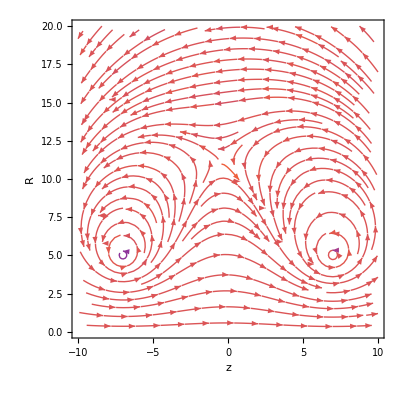

```mathematica
a =5;
const1=1;
const2 = 1.1;
current1=const1*(π/mu0);
current2 = const2*(π/mu0);
nZ = 10.;
nR = 20.;
StreamPlot[{fieldAxial[R,z]/Sqrt[fieldMagSqrd[R,z]],fieldRadial[R,z]/Sqrt[fieldMagSqrd[R,z]]},{z,-nZ,nZ},{R,0,nR},FrameLabel->{z,R},StreamColorFunction->Automatic,LabelStyle->{15,GrayLevel[0]},ImageSize->400]
```

```mathematica
D[EllipticK[m],m]
D[EllipticE[m],m]
```

## Solving ZGCM for second adiabatic invariant

47.157

{12.2572}

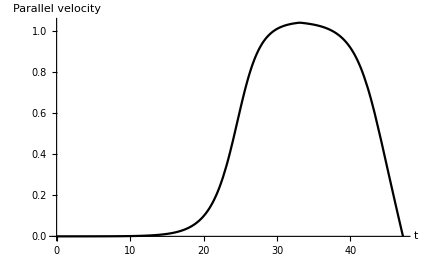

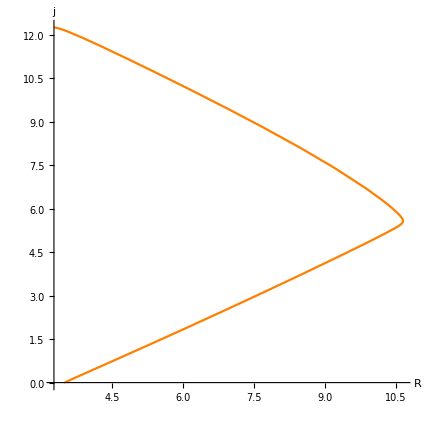

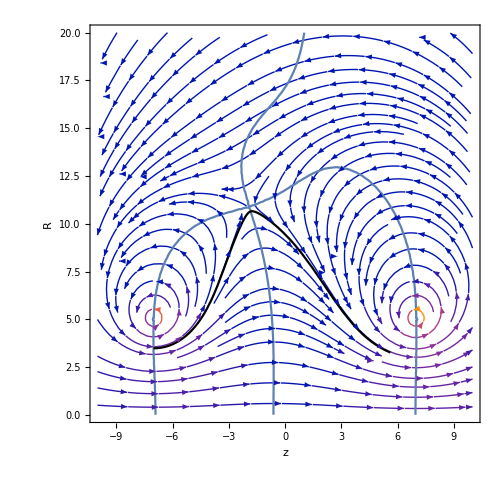

```mathematica
nZ = 10.;
nR = 20.;
mass = 1;
R0 =3.487;
Z0 =10^-4 + z/.With[{R =R0}, FindRoot[dfieldMagds[R,z] == 0,{{z,-7}}]] ;
tFinal = 300;
sol = NDSolve[{R'[t] == vPar[t]fieldRadial[R[t],Z[t]]/Sqrt[fieldMagSqrd[R[t],Z[t]]],Z'[t] == vPar[t]fieldAxial[R[t],Z[t]]/Sqrt[fieldMagSqrd[R[t],Z[t]]],vPar'[t] == - dfieldMagds[R[t],Z[t]],j'[t] == vPar[t]^2/Sqrt[2],R[0]==R0,Z[0] == Z0,vPar[0]==0.0,j[0] == 0,WhenEvent[vPar[t] == 0.0, Print[t];If[Abs[t]> 0.1,"StopIntegration"]]},{R,Z,vPar,j},{t,0,tFinal}];
(*sol = NDSolve[{R'[t] == vPar[t]fieldRadial[R[t],Z[t]]/Sqrt[fieldMagSqrd[R[t],Z[t]]],Z'[t] == vPar[t]fieldAxial[R[t],Z[t]]/Sqrt[fieldMagSqrd[R[t],Z[t]]],vPar'[t] == - dfieldMagds[R[t],Z[t]],j'[t] == vPar[t]^2/Sqrt[2],R[0]==R0,Z[0] == Z0,vPar[0]==0.0,j[0] == 0,WhenEvent[vPar[t] == 0.0, Print[t];{vPar[t]-> -vPar[t];j[t]->j0;t-> -t}]},{R,Z,vPar,j},{t,0,tFinal}];*)
tEnd=First[vPar/. sol][[1,-1]];
Print[j[tEnd[[2]]]/.sol]
vPlot = Plot[vPar[t]/.First[sol],{t,0,tEnd[[2]]},PlotStyle-> Black,AxesLabel->{t,Parallel velocity},LabelStyle->{15,GrayLevel[0]}]
(*vPlot = Plot[vPar[t]/.First[sol],{t,0,tFinal},PlotStyle-> Black,AxesLabel->{t,Parallel velocity},LabelStyle->{15,GrayLevel[0]}]*)
(*Export["/Users/OptimusPrime/Documents/magnetic-mirror/bounce_traj_vparallel.pdf",vPlot]*)
rzPlot =ParametricPlot[{Z[t],R[t]}/.First[sol],{t,0,tEnd[[2]]},PlotStyle -> {Black},AspectRatio->1,AxesLabel->{z,R},LabelStyle->{15,GrayLevel[0]}];
(*ParametricPlot[{Z[t],vPar[t]}/.First[sol],{t,0,tFinal},AspectRatio->1,AxesLabel->{z,Parallel velocity},LabelStyle->{15,GrayLevel[0]}]*)
jPlot = ParametricPlot[{R[t],j[t]}/.First[sol],{t,0,tEnd[[2]]},PlotStyle -> {Orange},AspectRatio->1,AxesLabel->{R,j},LabelStyle->{15,GrayLevel[0]}];
hPlot = ParametricPlot[{R[t],Sqrt[fieldMagSqrd[R[t],Z[t]]]}/.First[sol],{t,0,tEnd[[2]]},PlotStyle -> {Magenta},AspectRatio->1,AxesLabel->{R,"|B|"},LabelStyle->{15,GrayLevel[0]}];
Show[jPlot]
rzPlot = Show[bplot,sigmaplot,rzPlot]
(*Export["/Users/OptimusPrime/Documents/magnetic-mirror/bounce_traj_RZ_ex2.pdf",rzPlot]*)
```

{0.,91.5701}

0.01

38.5728

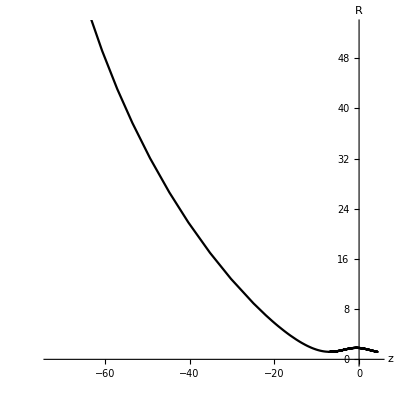

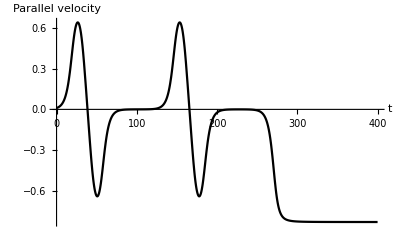

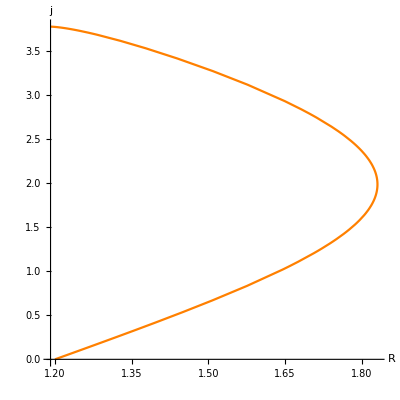

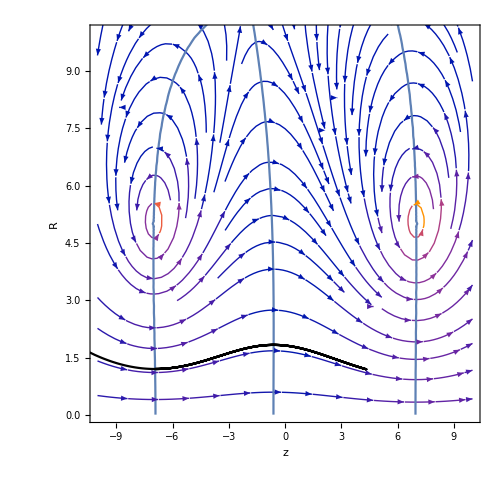

```mathematica
nZ = 10.;
nR = 20.;
mass = 1;
R0 = 1.2;
Z0 =z/.With[{R =R0}, FindRoot[dfieldMagds[R,z] == 0,{{z,-7}}]] ;
sTerm = 200;
tFinal = 400;
sol = NDSolve[{R'[s] == (v[s]*fieldRadial[R[s],Z[s]])/fieldMagSqrd[R[s],Z[s]],Z'[s] == (v[s]*fieldAxial[R[s],Z[s]])/fieldMagSqrd[R[s],Z[s]],v'[s] == -dfieldMagds[R[s],Z[s]]/Sqrt[fieldMagSqrd[R[s],Z[s]]],j'[s] ==- v[s]^2/(Sqrt[2*fieldMagSqrd[R[s],Z[s]]]),R[0]==R0,Z[0] == Z0,v[0]==0,j[0] == 0,WhenEvent[v[s] == 0.01,"StopIntegration"]},{R,Z,v,j},{s,0,sTerm}];
sEnd=First[v/. sol][[1,-1]]
R0 =R[sEnd[[2]]]/.First[sol];
Z0 = Z[sEnd[[2]]]/.First[sol];
v0 = v[sEnd[[2]]]/.First[sol]
j0 = j[sEnd[[2]]]/.First[sol];
{sol,tEvents} = Reap[NDSolve[{R'[t] == vPar[t]fieldRadial[R[t],Z[t]]/Sqrt[fieldMagSqrd[R[t],Z[t]]],Z'[t] == vPar[t]fieldAxial[R[t],Z[t]]/Sqrt[fieldMagSqrd[R[t],Z[t]]],vPar'[t] == - dfieldMagds[R[t],Z[t]],j'[t] == vPar[t]^2/Sqrt[2],R[0]==R0,Z[0] == Z0,vPar[0]==v0,j[0] == j0,WhenEvent[vPar[t] == 0.0, Sow[t,"Events"];{vPar[t]-> -vPar[t];t-> -t}]},{R,Z,vPar,j},{t,0,tFinal}]];
tEvents[[1,1]]
rzPlot =ParametricPlot[{Z[t],R[t]}/.First[sol],{t,0,tFinal},PlotStyle -> {Black},AspectRatio->1,AxesLabel->{z,R},LabelStyle->{15,GrayLevel[0]}]
 vPlot = Plot[vPar[t]/.First[sol],{t,0,tFinal},PlotStyle-> Black,AxesLabel->{t,Parallel velocity},LabelStyle->{15,GrayLevel[0]}]
(*Export["/Users/OptimusPrime/Documents/magnetic-mirror/bounce_traj_vparallel.pdf",vPlot]*)
jPlot = ParametricPlot[{R[t],j[t]}/.First[sol],{t,0,tEvents[[1,1]]},PlotStyle -> {Orange},AspectRatio->1,AxesLabel->{R,j},LabelStyle->{15,GrayLevel[0]}];
(*jPlot = Plot[j[t]/.First[sol],{t,0,tEvents[[1,1]]},PlotStyle -> {Orange},AspectRatio->1,AxesLabel->{R,j},LabelStyle->{15,GrayLevel[0]}];*)
hPlot = ParametricPlot[{R[t],Sqrt[fieldMagSqrd[R[t],Z[t]]]}/.First[sol],{t,0,tEvents[[1,1]]},PlotStyle -> {Magenta},AspectRatio->1,AxesLabel->{R,"|B|"},LabelStyle->{15,GrayLevel[0]}];
Show[jPlot]
(*Export["/Users/OptimusPrime/Documents/magnetic-mirror/bounce_traj_hR.pdf",hPlot]*)
rzPlot = Show[bplot,sigmaplot,rzPlot,PlotRange->{{-nZ,nZ},{0,10}}]
(*Export["/Users/OptimusPrime/Documents/magnetic-mirror/bounce_traj_RZ.pdf",rzPlot]*)
```

## Plotting field magnitude near left coil

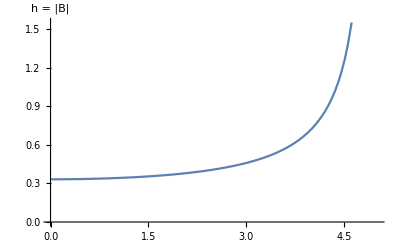

/Users/OptimusPrime/Documents/magnetic-mirror/honSigma_right1.5xleft.pdf

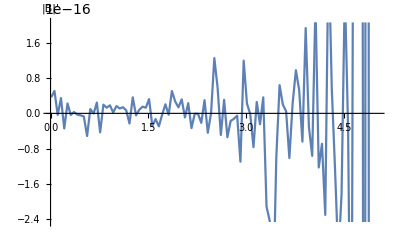

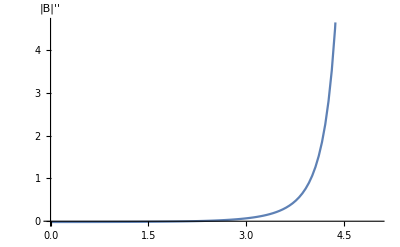

```mathematica
(*ri = 1;
zi =z/.With[{R =ri}, FindRoot[dfieldMagds[R,z] == 0,{{z,-7}}]] ;*)
fieldMagLeft = Table[{ri,zi = z/.With[{R =ri}, FindRoot[dfieldMagds[R,z] == 0,{z,-7}]] ;Sqrt[fieldMagSqrd[ri,zi]]},{ri,0.01,5.01,0.05}];
hvsRPlot = ListLinePlot[fieldMagLeft,AxesLabel->{"","h = |B|"},LabelStyle->{15,GrayLevel[0]}]
Export["/Users/OptimusPrime/Documents/magnetic-mirror/honSigma_right1.5xleft.pdf",hvsRPlot]
ListLinePlot[Table[{ri,zi = z/.With[{R =ri}, FindRoot[dfieldMagds[R,z] == 0,{{z,-7}}]] ;dfieldMagds[ri,zi]},{ri,0.01,5.01,0.05}],AxesLabel->{"","|B|'"},LabelStyle->{15,GrayLevel[0]}]
ListLinePlot[Table[{ri,zi = z/.With[{R =ri}, FindRoot[dfieldMagds[R,z] == 0,{{z,-7}}]] ;d2fieldMagds2[ri,zi]},{ri,0.01,5.01,0.05}],AxesLabel->{"","|B|''"},LabelStyle->{15,GrayLevel[0]}]
```

## Plotting j at first bounce

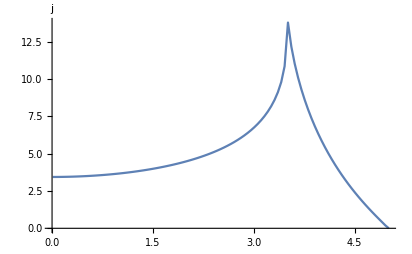

/Users/OptimusPrime/Documents/magnetic-mirror/jonSigma_right1.5xleft.pdf

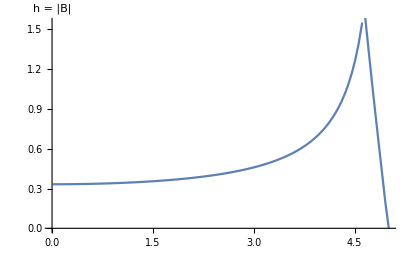

/Users/OptimusPrime/Documents/magnetic-mirror/honSigma_right1.5xleft.pdf

```mathematica
jFirstBounce = Table[{ri,R0 = ri;
Z0 =10^-3 + z/.With[{R =R0}, FindRoot[dfieldMagds[R,z] == 0,{{z,-7}}]] ;
tFinal = 500;
sol = NDSolve[{R'[t] == vPar[t]fieldRadial[R[t],Z[t]]/Sqrt[fieldMagSqrd[R[t],Z[t]]],Z'[t] == vPar[t]fieldAxial[R[t],Z[t]]/Sqrt[fieldMagSqrd[R[t],Z[t]]],vPar'[t] == - dfieldMagds[R[t],Z[t]],j'[t] == vPar[t]^2/Sqrt[2],R[0]==R0,Z[0] == Z0,vPar[0]==0.0,j[0] == 0,WhenEvent[vPar[t] == 0.0, If[Abs[t]> 0.1,"StopIntegration"]]},{R,Z,vPar,j},{t,0,tFinal}];
tEnd=First[vPar/. sol][[1,-1]];First[j[tEnd[[2]]]/.sol]},{ri,0.01,5.01,0.05}];
jvsRPlot=ListLinePlot[jFirstBounce,AxesLabel->{"","j"},LabelStyle->{15,GrayLevel[0]}]
Export["/Users/OptimusPrime/Documents/magnetic-mirror/jonSigma_right1.5xleft.pdf",jvsRPlot]
Show[hvsRPlot,jvsRPlot]
```

```mathematica
ri = 10;
zi/.With[{R =ri}, FindRoot[dfieldMagds[R,zi] == 0,{zi,-7.}]]
```

-5.38987

```mathematica
(*a =5;
const1=1;
const2 = 1;
current1=const1*(π/mu0);
current2 = const2*(π/mu0);
nZ = 10.;
nR = 20.;
mass = 1;
energy =3;
tFinalFirst = 0.1;
tFinal = 12;
R0 = 0.2; 
Z0 = -7;
vPerp = Sqrt[(2*energy)/mass] ;
μ = (mass*vPerp^2)/(2*Sqrt[fieldMagSqrd[R0,Z0]]);
solFirst= NDSolve[{R'[t] == fieldRadial[R[t],Z[t]],Z'[t] == fieldAxial[R[t],Z[t]],j'[t] == Sqrt[energy/μ- Sqrt[fieldMagSqrd[R[t],Z[t]]]]*Sqrt[fieldMagSqrd[R[t],Z[t]]],R[0]==R0,Z[0] == Z0,j[0] == 0},{R,Z,j},{t,0,tFinalFirst},MaxSteps-> ∞];
(*ParametricPlot[{Z[t],R[t]}/.sol,{t,0,tFinal},AspectRatio->1,AxesLabel->{z,R},LabelStyle->{15,GrayLevel[0]}]
Plot[{R[t],Z[t]}/.sol,{t,0,tFinal},PlotPoints-> 100,LabelStyle->{15,GrayLevel[0]}]*)
R0  = R[tFinalFirst]/.solFirst
Z0 = Z[tFinalFirst]/.solFirst
j0 = j[tFinalFirst]/.solFirst
vPar0 = Sqrt[(2/mass)*(energy - μ * Sqrt[fieldMagSqrd[R0,Z0]])]
(*vPar0 = Sqrt[2*(energy/((mass*vPerp)/(2*Sqrt[fieldMagSqrd[R0,Z0]])) - Sqrt[fieldMagSqrd[R0,Z0]])]*)
firstPlot = ParametricPlot[{Z[t],R[t]}/.solFirst,{t,0,tFinalFirst},AspectRatio->1,AxesLabel->{z,R},LabelStyle->{15,GrayLevel[0]}]*)
(*sol = NDSolve[{R'[t] == vPar[t]fieldRadial[R[t],Z[t]]/Sqrt[fieldMagSqrd[R[t],Z[t]]],Z'[t] == vPar[t]fieldAxial[R[t],Z[t]]/Sqrt[fieldMagSqrd[R[t],Z[t]]],vPar'[t] == -((2energy/mass - vPar[t]^2)/(2*Sqrt[fieldMagSqrd[R[t],Z[t]]]))* dfieldMagds[R[t],Z[t]],j'[t] == 0.5*vPar[t]^2,R[0]==R0,Z[0] == Z0,vPar[0]== vPar0,j[0] ==j0,WhenEvent[vPar[t] == 0.0,Print[t];If[Abs[t]> 1,"StopIntegration"]]},{R,Z,vPar,j},{t,tFinalFirst,tFinal},MaxSteps-> ∞];
secondPlot =ParametricPlot[{Z[t],R[t]}/.sol,{t,tFinalFirst,tFinal},AspectRatio->1,AxesLabel->{z,R},LabelStyle->{15,GrayLevel[0]}]
Plot[vPar[t]/.sol,{t,tFinalFirst,tFinal},PlotPoints-> 100,AxesLabel->{t,Parallel velocity},LabelStyle->{15,GrayLevel[0]}]*)
(*ParametricPlot[{Z[t],vPar[t]}/.sol,{t,0,tFinal},AspectRatio->1,AxesLabel->{z,Parallel velocity},LabelStyle->{15,GrayLevel[0]}]
ParametricPlot[{Z[t],j[t]}/.sol,{t,0,tFinal},AspectRatio->1,AxesLabel->{z,j},LabelStyle->{15,GrayLevel[0]}]*)
```